## Chapter 2 Problem 32: Finite Square Well

This problem is done in many undergraduate textbooks, but almost always using graphical interpretations to solve the necessary transcendental equations. In this solution, I’m trying to be more straightforward by making use of the techniques available in Mathematica. I’m not sure how successful I am, though.

```mathematica
Remove["Global`*"]
$Assumptions=α>0&&k>0&&a>0&&ℏ>0&& m>0&& η>0;
```

First let’s define the replacement statements for the quantities used in the wave functions. The energy eigenvalues are Ev, and the height of the walls is V_0=η ℏ^2/2 ma^2. We also write Ev=ϵV_0.

```mathematica
kRep=k->Sqrt[2 m Ev]/ℏ;
αRep=α->Sqrt[2m(V0-Ev)]/ℏ;
V0Rep=V0->η ℏ^2/(2m a^2);
EvRep=Ev->ϵ V0;
```

Set up the wave functions for the inside and left & right sides of the well. Note that even though we are taking k>0, switching k for -k in the “inside” wave function gives an equivalent form.

```mathematica
ψL=A Exp[α x];
ψI=B Exp[I k x]+C Exp[-I k x];
ψR=D Exp[-α x];
```

Set up the boundary condition equations, and display them as a column.

```mathematica
bceqs={
(ψL/.x->-a)==(ψI/.x->-a),
(ψR/.x->a)==(ψI/.x->a),
(D[ψL,x]/.x->-a)==(D[ψI,x]/.x->-a),
(D[ψR,x]/.x->a)==(D[ψI,x]/.x->a)};
MatrixForm[bceqs]
```

(A ⅇ^(-a α)==B ⅇ^(-ⅈ a k)+C ⅇ^(ⅈ a k)
D ⅇ^(-a α)==C ⅇ^(-ⅈ a k)+B ⅇ^(ⅈ a k)
A ⅇ^(-a α) α==ⅈ B ⅇ^(-ⅈ a k) k-ⅈ C ⅇ^(ⅈ a k) k
-D ⅇ^(-a α) α==-ⅈ C ⅇ^(-ⅈ a k) k+ⅈ B ⅇ^(ⅈ a k) k)

This can be written as a matrix M times the column vector of {A,B,C,D}, set equal to zero. In order to avoid the trivial solution, the determinant of M must be zero.

```mathematica
ABCD={A,B,C,D};
M=Normal[CoefficientArrays[bceqs,ABCD]][[2]];
MatrixForm[M]
```

(ⅇ^(-a α) | -ⅇ^(-ⅈ a k) | -ⅇ^(ⅈ a k) | 0
0 | -ⅇ^(ⅈ a k) | -ⅇ^(-ⅈ a k) | ⅇ^(-a α)
ⅇ^(-a α) α | -ⅈ ⅇ^(-ⅈ a k) k | ⅈ ⅇ^(ⅈ a k) k | 0
0 | -ⅈ ⅇ^(ⅈ a k) k | ⅈ ⅇ^(-ⅈ a k) k | -ⅇ^(-a α) α)

```mathematica
detM=FullSimplify[Det[M]]
```

ⅇ^(-2 a (ⅈ k+α)) (-ⅇ^(4 ⅈ a k) (k-ⅈ α)^2+(k+ⅈ α)^2)

There are obviously two choices that make the determinant zero, namely e^(2iak)(k-iα)=±(k+iα) which can be written as z=±z^* where z=e^iak(k-iα), so let’s try making that substitution.

```mathematica
Mz=M/.{Exp[I k a]->z/(k-I α),Exp[-I k a]->(k-I α)/z};
MzSol=Simplify[Solve[Det[Mz]==0,z]]
```

{{z→-√(k^2+α^2)},{z→-ⅈ √(k^2+α^2)},{z→ⅈ √(k^2+α^2)},{z→√(k^2+α^2)}}

We find four solutions, not two. Before trying to suss this out, let’s look at the wave functions that come out of each of these.

```mathematica
Mz1=Simplify[Mz/.MzSol[[1]]];
Mz1Sol=Solve[Mz1.ABCD==0,{B,C,D}];
B1=FullSimplify[B/.Mz1Sol];
C1=FullSimplify[C/.Mz1Sol];
D1=FullSimplify[D/.Mz1Sol];
```

```mathematica
ψI1=FullSimplify[ComplexExpand[ψI/.{B->B1,C->C1}]][[1]]
ψR1=FullSimplify[ψR/.{D->D1}][[1]]
```

-(A ⅇ^(-a α) √(k^2+α^2) Cos[k x])/k

A ⅇ^(-x α)

```mathematica
Mz2=Simplify[Mz/.MzSol[[2]]];
Mz2Sol=Solve[Mz2.ABCD==0,{B,C,D}];
B2=FullSimplify[B/.Mz2Sol];
C2=FullSimplify[C/.Mz2Sol];
D2=FullSimplify[D/.Mz2Sol];
```

```mathematica
ψI2=FullSimplify[ComplexExpand[ψI/.{B->B2,C->C2}]][[1]]
ψR2=FullSimplify[ψR/.{D->D2}][[1]]
```

(A ⅇ^(-a α) √(k^2+α^2) Sin[k x])/k

-A ⅇ^(-x α)

```mathematica
Mz3=Simplify[Mz/.MzSol[[3]]];
Mz3Sol=Solve[Mz3.ABCD==0,{B,C,D}];
B3=FullSimplify[B/.Mz3Sol];
C3=FullSimplify[C/.Mz3Sol];
D3=FullSimplify[D/.Mz3Sol];
```

```mathematica
ψI3=FullSimplify[ComplexExpand[ψI/.{B->B3,C->C3}]][[1]]
ψR3=FullSimplify[ψR/.{D->D3}][[1]]
```

-(A ⅇ^(-a α) √(k^2+α^2) Sin[k x])/k

-A ⅇ^(-x α)

```mathematica
Mz4=Simplify[Mz/.MzSol[[4]]];
Mz4Sol=Solve[Mz4.ABCD==0,{B,C,D}];
B4=FullSimplify[B/.Mz4Sol];
C4=FullSimplify[C/.Mz4Sol];
D4=FullSimplify[D/.Mz4Sol];
```

```mathematica
ψI4=FullSimplify[ComplexExpand[ψI/.{B->B4,C->C4}]][[1]]
ψR4=FullSimplify[ψR/.{D->D4}][[1]]
```

(A ⅇ^(-a α) √(k^2+α^2) Cos[k x])/k

A ⅇ^(-x α)

This is enlightening. In order to match the functions at x=+a, we would need k<0 for the first two solutions, but k>0 for the second two. We’ll take the latter and let k be positive. This can also be seen at the start by considering  z=z^*or z=-z^* with  z=re^(i(ka-ϕ)) where tanϕ = α/k and ka-ϕ equal to zero, π/2, π, or 3π/4.

We also see that the wave functions naturally separate into positive and negative parity solutions.

```mathematica
ψIPos=ψI4;
ψRPos=ψR4;
ψINeg=ψI3;
ψRNeg=ψR3;
```

Now we need to find the eigenvalues. Look at the boundary condition equations again, just working on the left side. Symmetry should give us the same result on the right, and setting the determinant equal to zero gives only one  equation for each solution.

```mathematica
eqkαPos=FullSimplify[
FullSimplify[bceqs[[1]]/.{B->B4[[1]],C->C4[[1]],D->D4[[1]]},A>0]
/.kRep/.αRep/.EvRep/.V0Rep]
```

√(ϵ η)==√η Cos[√(ϵ η)]

```mathematica
eqkαNeg=FullSimplify[
FullSimplify[bceqs[[1]]/.{B->B3[[1]],C->C3[[1]],D->D3[[1]]},A>0]
/.kRep/.αRep/.EvRep/.V0Rep]
```

√(ϵ η)==√η Sin[√(ϵ η)]

Recall that η gives the value for V_0 in terms of ℏ^2/2 ma^2 and ϵ is the energy eigenvalue in terms of V_0 so must be between zero and unity for a bound state. Notice that for a very shallow well (small η) the positive parity case will always find a solution:

```mathematica
ϵs=δ^2/.Solve[Normal[Series[Simplify[eqkαPos/.ϵ->δ^2,δ>0],{η,0,1}]],δ];
Normal[Series[ϵs,{η,0,1}]]
```

{-1+4/η^2+4/η+η,1-η}

That is, the second list element is an eigenvalue will always be positive and ϵ<1 for small η. However, the negative parity case, for small η, cannot be solved, as it reduces to 1=Sqrt[η].

Now let’s make a plot of the boundary equation solutions and then solve numerically for the eigenvalues.  At this point we need to get numerical, so insert the appropriate value of η for the given problem.

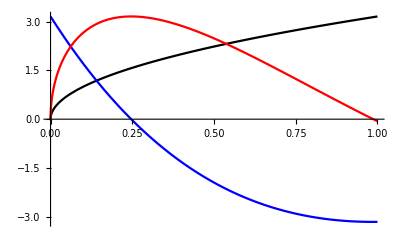

```mathematica
ηVal=10;
Plot[{eqkαPos[[1]]/.η->ηVal,eqkαPos[[2]]/.η->ηVal,eqkαNeg[[2]]/.η->ηVal},{ϵ,0,1},PlotStyle->{Black,Blue,Red}]
```

Clearly there are two energy eigenvalues, one for the positive and one for the negative parity cases

```mathematica
ϵPos=FindRoot[eqkαPos/.η->ηVal,{ϵ,0.2}]
ϵNeg=FindRoot[eqkαNeg/.η->ηVal,{ϵ,0.5}]
```

{ϵ→0.140721}

{ϵ→0.537581}

Now build and plot the two wave functions, including normalizations

```mathematica
ψPos=Piecewise[{{ψL,x<-a},{ψIPos,-a<x<a},{ψRPos,x>a}}];
ψNeg=Piecewise[{{ψL,x<-a},{ψINeg,-a<x<a},{ψRNeg,x>a}}];
```

```mathematica
ψPosPlot=Simplify[ψPos/.kRep/.αRep/.EvRep/.V0Rep/.η->ηVal/.x->u a/.ϵPos];
ψNegPlot=Simplify[ψNeg/.kRep/.αRep/.EvRep/.V0Rep/.η->ηVal/.x->u a/.ϵNeg];
```

```mathematica
APos=A/.Solve[Integrate[ψPosPlot^2,{u,-∞,+∞}]==1,A][[2]]
ANeg=A/.Solve[Integrate[ψNegPlot^2,{u,-∞,+∞}]==1,A][[2]]
```

6.07449

5.20239

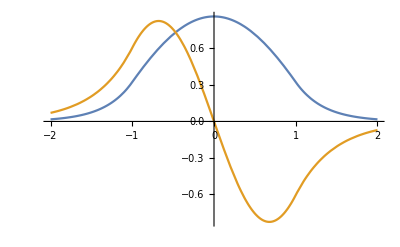

```mathematica
Plot[{ψPosPlot/.A->APos,ψNegPlot/.A->ANeg},{u,-2,2}]
```